# Problem 3, A route to chaos

## for February 09, 23.59, 2024

## The dynamics of a population with adults cannibalising on their offspring can be described by the Ricker map where denotes the number of adults in generation , while is related to the number of offspring produced by each adult and α is the incidence rate of cannibalism. The factor describes the probability of offspring survival to maturity. In this task you will analyse the stability of the steady states of the Ricker map as a function of the parameter for α = 0.01 and .

## a) Assume that takes the values from 1 to 30 in steps of 0.1 and plot the bifurcation diagram of η against as follows. For each value of , run the model for 300 generations and plot the last 100 values of versus the value of . The final plot should show the results for all values of tested. Describe the result.

```mathematica
ClearAll["Global`*"];
MaxGeneration = 300;
η = 900;
α = 0.01;

dataPoints = Table[
	(* First data will be created using NestList and then the first 200 data points are dropped.*)
    data = Drop[NestList[R*(#)*Exp[-(α*(#))] &, η, MaxGeneration], 200];
    (* Now the data which is a list of values is changed to a list of list with two elements {{R, dataPoint1}, {R, dataPoint2}, ...} *)
    pairedData = Map[{R, #} &, data];
    {R, pairedData},
    {R, 1, 30, 0.1}];

ListPlot[dataPoints[[All, 2]], 
 AxesLabel -> {"R", ""}, 
 PlotRange -> All,
 PlotLabel->"Amount of adults after 300 generations (η_300) depending on the quasi-rate of reproduction (R)",
 ImageSize->{500,300}]
```

In the plot we can see fractal behaviour, with infinite period doubling. Each point on the map corresponds to a cycle starting with a fixed point (1-point cycle) until  then a 2-point cycle start and goes over to a 4-point cycle around . This doubling goes on until  is reached where the period is infinite. If one overshoots this  the full period doubling pattern reappears in small windows of the plot ().

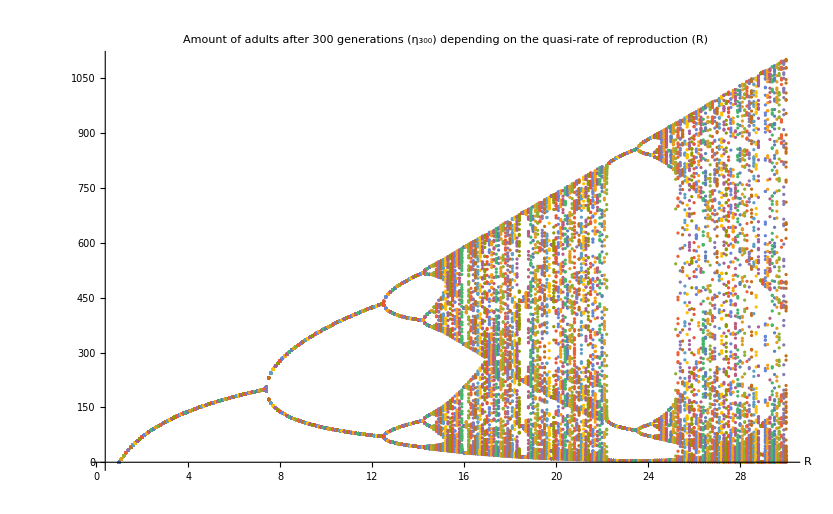

## b) Plot the population dynamics versus τ (where τ = 0, . . . , 40) for four values of . Choose four representative values of where has a stable fixed point, a 2-point cycle. a 3-point cycle, and a 4-point cycle. Describe the dynamics observed for the four values of .

I found a stable fixed point for the value of = 5, a 2-point cycle for , a 3-point cycle for  and a 5-point cycle for .

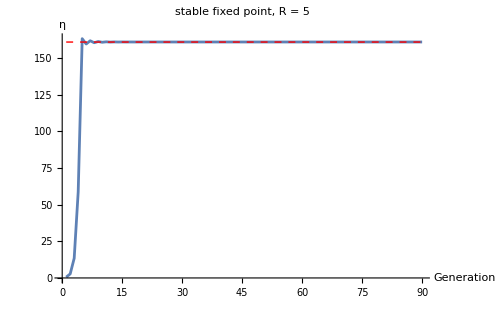

```mathematica
ClearAll["Global`*"];
η = 900;
α = 0.01;
R = 5;

dataPoints = Table[
    data = Drop[NestList[R*(#)*Exp[-(α*(#))] &, η, MaxGeneration], MaxGeneration];
    pairedData = MapIndexed[{First[#2] + MaxGeneration - Length[data], #1} &, data];
    pairedData,
    {MaxGeneration, 1, 90, 1}];

ListPlot[Flatten[dataPoints, 1], 
 AxesLabel -> {"Generation", "η"}, 
 PlotRange -> All, 
 PlotLabel -> "stable fixed point, R = 5",
 Joined -> True,
  Epilog -> {
  Red, Dashed,Line[{{1, 160.9}, {90, 160.9}}]},
  ImageSize->{500,300}
  ]
```

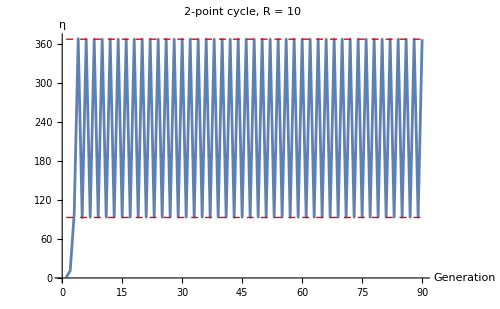

```mathematica
ClearAll["Global`*"];
η = 900;
α = 0.01;
R = 10;

dataPoints = Table[
    data = Drop[NestList[R*(#)*Exp[-(α*(#))] &, η, MaxGeneration], MaxGeneration];
    pairedData = MapIndexed[{First[#2] + MaxGeneration - Length[data], #1} &, data];
    pairedData,
    {MaxGeneration, 1, 90, 1}];

ListPlot[Flatten[dataPoints, 1], 
 AxesLabel -> {"Generation", "η"}, 
 PlotRange -> All, 
 PlotLabel -> "2-point cycle, R = 10",
 Joined -> True,
  Epilog -> {
  Red, Dashed, Line[{{1, 93}, {90, 93}}],Line[{{1, 367}, {90, 367}}]},
  ImageSize->{500,300}
  ]
```

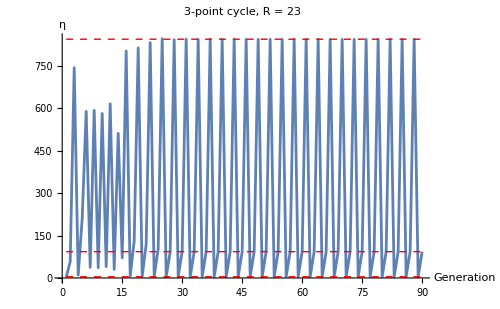

```mathematica
ClearAll["Global`*"];
η = 900;
α = 0.01;
R = 23;

dataPoints = Table[
    data = Drop[NestList[R*(#)*Exp[-(α*(#))] &, η, MaxGeneration], MaxGeneration];
    pairedData = MapIndexed[{First[#2] + MaxGeneration - Length[data], #1} &, data];
    pairedData,
    {MaxGeneration, 1, 90, 1}];

ListPlot[Flatten[dataPoints, 1], 
 AxesLabel -> {"Generation", "η"}, 
 PlotRange -> All, 
 PlotLabel -> "3-point cycle, R = 23",
 Joined -> True,
  Epilog -> {
  Red, Dashed, Line[{{1, 844}, {90, 844}}],Line[{{1, 93}, {90, 93}}], Line[{{1, 4}, {90, 4}}]},
  ImageSize->{500,300}
  ]
```

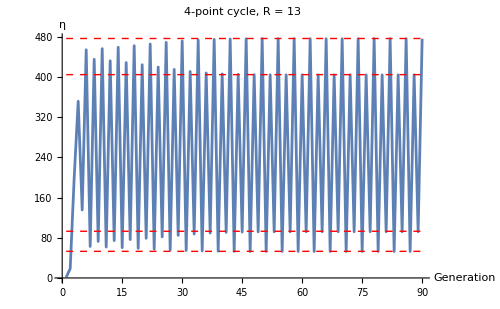

```mathematica
ClearAll["Global`*"];
η = 900;
α = 0.01;
R = 13;

dataPoints = Table[
    data = Drop[NestList[R*(#)*Exp[-(α*(#))] &, η, MaxGeneration], MaxGeneration];
    pairedData = MapIndexed[{First[#2] + MaxGeneration - Length[data], #1} &, data];
    pairedData,
    {MaxGeneration, 1, 90, 1}];

ListPlot[Flatten[dataPoints, 1], 
 AxesLabel -> {"Generation", "η"}, 
 PlotRange -> All, 
 PlotLabel -> "4-point cycle, R = 13",
 Joined -> True,
  Epilog -> {
  Red, Dashed, Line[{{1, 477}, {90, 477}}],Line[{{1, 93}, {90, 93}}], Line[{{1, 53}, {90, 53}}], Line[{{1, 405}, {90, 405}}]},
  ImageSize->{500,300}
  ]
```

## c) Investigating the plot in subtask a), at which value of does the population dynamics bifurcate from a stable equilibrium to a stable 2-point cycle? At which value does the dynamics bifurcate to a stable 4-point cycle?

From the plot of a) it looks like that for  the bifurcation happens and goes over to a stable 2-point cycle, while the 4-point cycle appears for .

## d) By making zooms and refining the -grid, make a rough estimate of , the first parameter value where the period-doubling bifurcation has repeated an infinite number of times. Explain how you come to this estimate of .

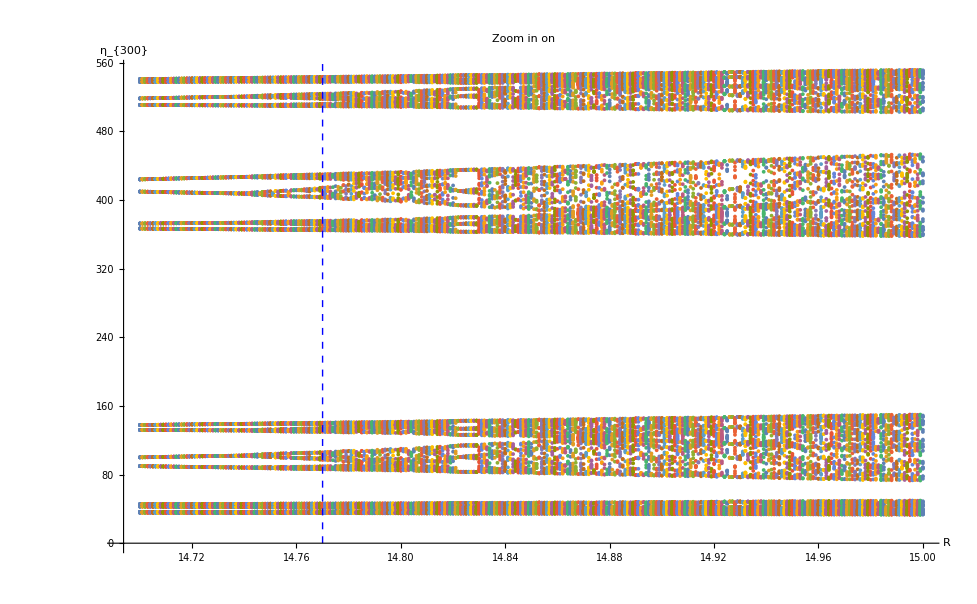

```mathematica
ClearAll["Global`*"];
MaxGeneration = 300;
η = 900;
α = 0.01;

dataPoints = Table[
	(* First data will be created using NestList and then the first 200 data points are dropped.*)
    data = Drop[NestList[R*(#)*Exp[-(α*(#))] &, η, MaxGeneration], 200];
    (* Now the data which is a list of values is changed to a list of list with two elements {{R, dataPoint1}, {R, dataPoint2}, ...} *)
    pairedData = Map[{R, #} &, data];
    {R, pairedData},
    {R, 14.7, 15, 0.001}];

ListPlot[dataPoints[[All, 2]], 
 AxesLabel -> {"R", "η_{300}"}, 
 PlotRange -> All,
 PlotLabel -> "Zoom in on ",
 Epilog -> {Blue, Dashed, Line[{{14.77, 0}, {14.77, 600}}]},
 ImageSize->{500,300}
]
```

My guesstimate for the  is around . This because that is where the pockets close for the first time. When they close the period doubling has happened an infinite amount of times.